```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/675nm.dat"]
```

{{1.59376,0.171176},{1.5163,0.193344},{1.45822,0.192684},{1.41492,0.178899},{1.36475,0.18648},{1.33366,0.200407},{1.2821,0.198031},{1.25075,0.195896},{1.2275,0.189794},{1.20277,0.191612},{1.18632,0.199916},{1.16701,0.191116},{1.14926,0.17185},{1.12973,0.111094},{1.10588,-1.59229},{1.11907,0.105531},{1.13878,0.218412},{1.30525,0.197621},{1.35407,0.149712}}

-1.03444+0.876774 x

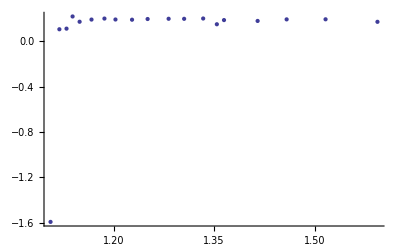

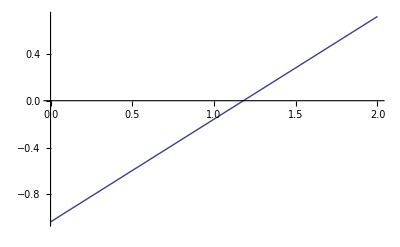

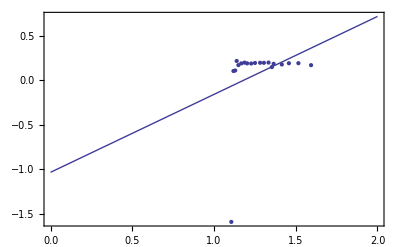

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```